# Evolutionary Dynamics under Linear Returns

```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]];
```

## 1. Functions

```mathematica
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
Functions = { Bc->Function[k,n (k/n)^u β]};
```

```mathematica
values={n->4,β->1,Cc-> 0.3,δ->1,u->1,cd-> 0.5} ;

cm=72/2.54;
```

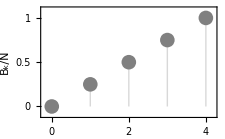

```mathematica
graphicspPayoffs=ListPlot[Table[{k,(k/n)^u β  }/.values,{k,0,4}],Filling->Axis,PlotStyle->Gray,Frame->True,FrameTicks->{{{0,0.5,1},None},{{0,1,2,3,4},None}},ImageSize->8cm,FrameLabel->{k,Rotate[Subscript[B, k]/N,-Pi/2]},LabelStyle->Directive[FontFamily->"Arial",FontSize->17,Black],PlotMarkers->{Automatic,15},PlotRange-> {{-0.2,4.2},{-0.1,1.1}}]
```

Figure 3a of the main text

```mathematica
Export["Payoff_Linear.pdf",Show[graphicspPayoffs,ImageSize->8 cm]]
```

Payoff_Linear.pdf

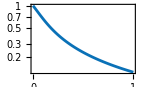

```mathematica
graphicspUnconditionalD=LogPlot[{2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))}/.n-> 4,{cd,0,1},PlotStyle->blue,Frame->True,FrameTicks->{{{0,0.2,.5,1},None},{{0,0.5,1},None}},ImageSize->5 cm,FrameLabel->{Subscript[c, d],SuperStar[d]},LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Black],PlotRange-> {{0,1},{0,1}},RotateLabel->False]
```

Figure 3b of the main text

```mathematica
Export["dispersal.pdf",Show[graphicspUnconditionalD,ImageSize->5 cm]]
```

```mathematica
dispersal.pdf"
```

## 2. Tracking the evolutionary dynamics through time (Figure 3c)

This numerical analyses iterates a perturbation in the direction of the selection gradient vector on the population traits' values. We start from a population of  defectors expressing initial phenotypic value z0={d^*, 0.4, 0.6, 0.7, 0.9, 0}. It stops the iteration once the population expresses z = 0 or z = 1 (here z=1). This corresponds to the procedure described in Appendix D.1.

```mathematica
values={n->4,β->1,Cc-> 0.3,δ->1,u->1,cd-> 0.5} ;
ntest = n /. values;
cdtest = cd  /. values;
utest = u /. values;
valuesNeutral={n->ntest,β->0,Cc-> 0,cd->cdtest,u-> utest} ;
m[k_]:=fecdisp[d[n+1]] /(fecpatch[k](1-d[k])+fecdisp[d[n+1]] )/.δ->0;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.Functions//.values;
solR2=Flatten[Solve[(R2 == ∑_(c0=0)^n (1-m[c0])^2(1/n+(n-1)/n R2)Pk0[c0,d[n+1],n]/.valuesNeutral/.Functions//.valuesNeutral),R2]];
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
(* number of offspring coming into an arbirary patch when the population is monomorphic for z *)

w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.values/.Functions//.values;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,ntest+1},{i,1,3}]];
S=
Table[
D[w, d[1,k]]+ (n-1)R2 D[w, d[2,k]]/. solR2 /. monopop /.Functions//.values
,{k,0,ntest+1}];
Δz[u_]:=Clip[ u+G.(S/. Table[d[k]-> u[[1+k]],{k,0,ntest+1}] ),{0.,1.}];
z0 = {d0baseline,0.4,0.6,0.7,0.9,0};
G =0.1 IdentityMatrix[ntest+2];
res = NestWhileList[Δz,z0,EuclideanDistance[#1,#2]>10^-8&,2,5000];
```

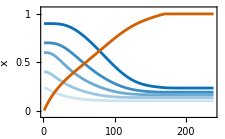

```mathematica
p1=ListLinePlot[Flatten[res,{2}][[1;;ntest+1]],PlotRange->{0,1}, PlotStyle->Map[Lighter[blue,#]&,Reverse[Range[0,0.8,N[0.8/(ntest)]]]]];
p2=ListLinePlot[Flatten[res,{2}][[ntest+2]],PlotRange->{0,1},PlotStyle->Directive[orange]];
Show[p1,p2,Frame->True,FrameTicks->{{{0,.5,1},None},{{0,100,200},None}},ImageSize->8 cm,FrameLabel->{"generation",x̄},LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Black],PlotRange->{-0.05,1.05},RotateLabel->False]
```

```mathematica
Export["Cooperation_Invade.pdf",Show[Show[p1,p2,Frame->True,FrameTicks->{{{0,.5,1},None},{{0,100,200},None}},ImageSize->8 cm,FrameLabel->{"generation",x̄},LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Black],PlotRange->{-0.05,1.05},RotateLabel->False],ImageSize->8 cm]]
```

Cooperation_Invade.pdf

## 3. Basin of attraction for full and loss of cooperation

### 3.1 Fixation of cooperation from rarity

We repeat the process described above for 100 different initial dispersal values, with d_0=d^*,d_1 taking value between 0 and 1, and d_2, d_3and d_4 chosen at random. We keep track of the proportion of initial conditions that lead to z=1. This procedure is described in Appendix D.2. As this procedure takes some computational time, we present the results generated from this procedure when plotting Fig. 3d.

```mathematica
NumericAnalysesInvade=Table[
Print[cdi];
values={n->4,β->1,Cc-> 0.3,δ->1.,u->1.,cd-> cdi} ;
ntest = n /. values;
cdtest = cd  /. values;
utest = u /. values;
valuesNeutral={n->ntest,β->0,Cc-> 0,cd->cdtest,u-> utest} ;
m[k_]:=fecdisp[d[n+1]] /(fecpatch[k](1-d[k])+fecdisp[d[n+1]] )/.δ->0;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.values;
solR2=Flatten[Solve[(R2 == ∑_(c0=0)^n (1-m[c0])^2(1/n+((n-1)/n)R2)Pk0[c0,d[n+1],n]/.valuesNeutral/.Functions//.valuesNeutral),R2]];
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) ;(* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.values/.Functions//.values;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,ntest+1},{i,1,3}]];
S=
Table[
D[w, d[1,k]]+ (n-1)R2 D[w, d[2,k]]/. solR2 /. monopop /.values
,{k,0,ntest+1}];
Table[
res=
ParallelTable[
z0Random=Append[ Table[ RandomReal[{10^-5,1-10^-5}],{k,1,ntest+1}] ,0.];
z0= z0Random;
z0[[1]]= d0baseline;
z0[[2]]=d1;
G =0.1 IdentityMatrix[ntest+2];
Δz[u_]:=Clip[ u+G.(S/. Table[d[k]-> u[[1+k]],{k,0,ntest+1}] ),{0.,1.}];
ngenmax=5000;
res0=NestWhile[Δz,z0,Abs[#1[[ntest+2]]-#2[[ntest+2]]]>10^-8&,2,ngenmax];
fix0=Last[res0];
Round[fix0,0.1]
,
{i,100}];
{cdi,d1,Mean[res]} 
,{d1,0.05,0.95,0.05}],{cdi,0.05,0.95,0.05}
]
NumericAnalysesInvade=Flatten[NumericAnalysesInvade,1]
```

```mathematica
(* This is the result we obtained running the above function once with 100 sets of initial trait values for each value of d1 and cd. If you run the above function, your results may differ slightly (due to the fact that the initial trait values will differ)*)
NumericAnalysesInvade={{0.05,0.05,0.},{0.05,0.1,0.},{0.05,0.15,0.},{0.05,0.2,0.},{0.05,0.25,0.},{0.05,0.3,0.},{0.05,0.35,0.},{0.05,0.4,0.},{0.05,0.45,0.},{0.05,0.5,0.},{0.05,0.55,0.},{0.05,0.6,0.},{0.05,0.65,0.},{0.05,0.7,0.},{0.05,0.75,0.},{0.05,0.8,0.},{0.05,0.85,0.},{0.05,0.9,0.},{0.05,0.95,0.},{0.1,0.05,0.},{0.1,0.1,0.},{0.1,0.15,0.},{0.1,0.2,0.},{0.1,0.25,0.},{0.1,0.3,0.},{0.1,0.35,0.},{0.1,0.4,0.},{0.1,0.45,0.},{0.1,0.5,0.},{0.1,0.55,0.},{0.1,0.6,0.},{0.1,0.65,0.},{0.1,0.7,0.},{0.1,0.75,0.},{0.1,0.8,0.},{0.1,0.85,0.},{0.1,0.9,0.},{0.1,0.95,0.},{0.15,0.05,0.},{0.15,0.1,0.},{0.15,0.15,0.},{0.15,0.2,0.},{0.15,0.25,0.},{0.15,0.3,0.},{0.15,0.35,0.},{0.15,0.4,0.},{0.15,0.45,0.},{0.15,0.5,0.},{0.15,0.55,0.},{0.15,0.6,0.},{0.15,0.65,0.},{0.15,0.7,0.},{0.15,0.75,0.},{0.15,0.8,0.},{0.15,0.85,0.},{0.15,0.9,0.},{0.15,0.95,0.},{0.2,0.05,0.},{0.2,0.1,0.},{0.2,0.15,0.},{0.2,0.2,0.},{0.2,0.25,0.},{0.2,0.3,0.},{0.2,0.35,0.},{0.2,0.4,0.},{0.2,0.45,0.},{0.2,0.5,0.},{0.2,0.55,0.735},{0.2,0.6,0.764},{0.2,0.65,0.739},{0.2,0.7,0.777},{0.2,0.75,0.757},{0.2,0.8,0.78},{0.2,0.85,0.842},{0.2,0.9,0.724},{0.2,0.95,0.},{0.25,0.05,0.},{0.25,0.1,0.},{0.25,0.15,0.},{0.25,0.2,0.},{0.25,0.25,0.},{0.25,0.3,0.},{0.25,0.35,0.},{0.25,0.4,0.},{0.25,0.45,1.},{0.25,0.5,0.98},{0.25,0.55,0.99},{0.25,0.6,1.},{0.25,0.65,0.98},{0.25,0.7,1.},{0.25,0.75,0.99},{0.25,0.8,1.},{0.25,0.85,1.},{0.25,0.9,0.99},{0.25,0.95,0.},{0.3,0.05,0.},{0.3,0.1,0.},{0.3,0.15,0.},{0.3,0.2,0.},{0.3,0.25,0.},{0.3,0.3,0.},{0.3,0.35,0.},{0.3,0.4,1.},{0.3,0.45,1.},{0.3,0.5,1.},{0.3,0.55,1.},{0.3,0.6,1.},{0.3,0.65,1.},{0.3,0.7,1.},{0.3,0.75,1.},{0.3,0.8,1.},{0.3,0.85,1.},{0.3,0.9,1.},{0.3,0.95,0.},{0.35,0.05,0.},{0.35,0.1,0.},{0.35,0.15,0.},{0.35,0.2,0.},{0.35,0.25,0.},{0.35,0.3,0.},{0.35,0.35,1.},{0.35,0.4,1.},{0.35,0.45,1.},{0.35,0.5,1.},{0.35,0.55,1.},{0.35,0.6,1.},{0.35,0.65,1.},{0.35,0.7,1.},{0.35,0.75,1.},{0.35,0.8,1.},{0.35,0.85,1.},{0.35,0.9,1.},{0.35,0.95,0.},{0.4,0.05,0.},{0.4,0.1,0.},{0.4,0.15,0.},{0.4,0.2,0.},{0.4,0.25,0.},{0.4,0.3,0.},{0.4,0.35,1.},{0.4,0.4,1.},{0.4,0.45,1.},{0.4,0.5,1.},{0.4,0.55,1.},{0.4,0.6,1.},{0.4,0.65,1.},{0.4,0.7,1.},{0.4,0.75,1.},{0.4,0.8,1.},{0.4,0.85,1.},{0.4,0.9,1.},{0.4,0.95,0.},{0.45,0.05,0.},{0.45,0.1,0.},{0.45,0.15,0.},{0.45,0.2,0.},{0.45,0.25,0.},{0.45,0.3,1.},{0.45,0.35,1.},{0.45,0.4,1.},{0.45,0.45,1.},{0.45,0.5,1.},{0.45,0.55,1.},{0.45,0.6,1.},{0.45,0.65,1.},{0.45,0.7,1.},{0.45,0.75,1.},{0.45,0.8,1.},{0.45,0.85,1.},{0.45,0.9,1.},{0.45,0.95,0.},{0.5,0.05,0.},{0.5,0.1,0.},{0.5,0.15,0.},{0.5,0.2,0.},{0.5,0.25,1.},{0.5,0.3,1.},{0.5,0.35,1.},{0.5,0.4,1.},{0.5,0.45,1.},{0.5,0.5,1.},{0.5,0.55,1.},{0.5,0.6,1.},{0.5,0.65,1.},{0.5,0.7,1.},{0.5,0.75,1.},{0.5,0.8,1.},{0.5,0.85,1.},{0.5,0.9,1.},{0.5,0.95,0.},{0.55,0.05,0.},{0.55,0.1,0.},{0.55,0.15,0.},{0.55,0.2,0.},{0.55,0.25,1.},{0.55,0.3,1.},{0.55,0.35,1.},{0.55,0.4,1.},{0.55,0.45,1.},{0.55,0.5,1.},{0.55,0.55,1.},{0.55,0.6,1.},{0.55,0.65,1.},{0.55,0.7,1.},{0.55,0.75,1.},{0.55,0.8,1.},{0.55,0.85,1.},{0.55,0.9,1.},{0.55,0.95,0.},{0.6,0.05,0.},{0.6,0.1,0.},{0.6,0.15,0.},{0.6,0.2,0.},{0.6,0.25,1.},{0.6,0.3,1.},{0.6,0.35,1.},{0.6,0.4,1.},{0.6,0.45,1.},{0.6,0.5,1.},{0.6,0.55,1.},{0.6,0.6,1.},{0.6,0.65,1.},{0.6,0.7,1.},{0.6,0.75,1.},{0.6,0.8,1.},{0.6,0.85,1.},{0.6,0.9,1.},{0.6,0.95,0.},{0.65,0.05,0.},{0.65,0.1,0.},{0.65,0.15,0.},{0.65,0.2,1.},{0.65,0.25,1.},{0.65,0.3,1.},{0.65,0.35,1.},{0.65,0.4,1.},{0.65,0.45,1.},{0.65,0.5,1.},{0.65,0.55,1.},{0.65,0.6,1.},{0.65,0.65,1.},{0.65,0.7,1.},{0.65,0.75,1.},{0.65,0.8,1.},{0.65,0.85,1.},{0.65,0.9,1.},{0.65,0.95,0.},{0.7,0.05,0.},{0.7,0.1,0.},{0.7,0.15,0.},{0.7,0.2,1.},{0.7,0.25,1.},{0.7,0.3,1.},{0.7,0.35,1.},{0.7,0.4,1.},{0.7,0.45,1.},{0.7,0.5,1.},{0.7,0.55,1.},{0.7,0.6,1.},{0.7,0.65,1.},{0.7,0.7,1.},{0.7,0.75,1.},{0.7,0.8,1.},{0.7,0.85,1.},{0.7,0.9,1.},{0.7,0.95,0.},{0.75,0.05,0.},{0.75,0.1,0.},{0.75,0.15,0.},{0.75,0.2,1.},{0.75,0.25,1.},{0.75,0.3,1.},{0.75,0.35,1.},{0.75,0.4,1.},{0.75,0.45,1.},{0.75,0.5,1.},{0.75,0.55,1.},{0.75,0.6,1.},{0.75,0.65,1.},{0.75,0.7,1.},{0.75,0.75,1.},{0.75,0.8,1.},{0.75,0.85,1.},{0.75,0.9,1.},{0.75,0.95,0.},{0.8,0.05,0.},{0.8,0.1,0.},{0.8,0.15,0.},{0.8,0.2,1.},{0.8,0.25,1.},{0.8,0.3,1.},{0.8,0.35,1.},{0.8,0.4,1.},{0.8,0.45,1.},{0.8,0.5,1.},{0.8,0.55,1.},{0.8,0.6,1.},{0.8,0.65,1.},{0.8,0.7,1.},{0.8,0.75,1.},{0.8,0.8,1.},{0.8,0.85,1.},{0.8,0.9,1.},{0.8,0.95,0.},{0.85,0.05,0.},{0.85,0.1,0.},{0.85,0.15,0.},{0.85,0.2,1.},{0.85,0.25,1.},{0.85,0.3,1.},{0.85,0.35,1.},{0.85,0.4,1.},{0.85,0.45,1.},{0.85,0.5,1.},{0.85,0.55,1.},{0.85,0.6,1.},{0.85,0.65,1.},{0.85,0.7,1.},{0.85,0.75,1.},{0.85,0.8,1.},{0.85,0.85,1.},{0.85,0.9,1.},{0.85,0.95,0.},{0.9,0.05,0.},{0.9,0.1,0.},{0.9,0.15,1.},{0.9,0.2,1.},{0.9,0.25,1.},{0.9,0.3,1.},{0.9,0.35,1.},{0.9,0.4,1.},{0.9,0.45,1.},{0.9,0.5,1.},{0.9,0.55,1.},{0.9,0.6,1.},{0.9,0.65,1.},{0.9,0.7,1.},{0.9,0.75,1.},{0.9,0.8,1.},{0.9,0.85,1.},{0.9,0.9,1.},{0.9,0.95,0.},{0.95,0.05,0.},{0.95,0.1,0.},{0.95,0.15,1.},{0.95,0.2,1.},{0.95,0.25,1.},{0.95,0.3,1.},{0.95,0.35,1.},{0.95,0.4,1.},{0.95,0.45,1.},{0.95,0.5,1.},{0.95,0.55,1.},{0.95,0.6,1.},{0.95,0.65,1.},{0.95,0.7,1.},{0.95,0.75,1.},{0.95,0.8,1.},{0.95,0.85,1.},{0.95,0.9,1.},{0.95,0.95,0.},{0.05,0.01,0.},{0.05,0.99,0.},{0.1,0.01,0.},{0.1,0.99,0.},{0.15,0.01,0.},{0.15,0.99,0.},{0.2,0.01,0.},{0.2,0.99,0.},{0.25,0.01,0.},{0.25,0.99,0.},{0.3,0.01,0.},{0.3,0.99,0.},{0.35,0.01,0.},{0.35,0.99,0.},{0.4,0.01,0.},{0.4,0.99,0.},{0.45,0.01,0.},{0.45,0.99,0.},{0.5,0.01,0.},{0.5,0.99,0.},{0.55,0.01,0.},{0.55,0.99,0.},{0.6,0.01,0.},{0.6,0.99,0.},{0.65,0.01,0.},{0.65,0.99,0.},{0.7,0.01,0.},{0.7,0.99,0.},{0.75,0.01,0.},{0.75,0.99,0.},{0.8,0.01,0.},{0.8,0.99,0.},{0.85,0.01,0.},{0.85,0.99,0.},{0.9,0.01,0.},{0.9,0.99,0.},{0.95,0.01,0.},{0.95,0.99,0.},{0.01,0.05,0.},{0.01,0.1,0.},{0.01,0.15,0.},{0.01,0.2,0.},{0.01,0.25,0.},{0.01,0.3,0.},{0.01,0.35,0.},{0.01,0.4,0.},{0.01,0.45,0.},{0.01,0.5,0.},{0.01,0.55,0.},{0.01,0.6,0.},{0.01,0.65,0.},{0.01,0.7,0.},{0.01,0.75,0.},{0.01,0.8,0.},{0.01,0.85,0.},{0.01,0.9,0.},{0.01,0.95,0.},{0.05,0.92,0.},{0.1,0.92,0.},{0.15,0.92,0.},{0.2,0.92,0.798},{0.25,0.92,1.},{0.3,0.92,1.},{0.35,0.92,1.},{0.4,0.92,1.},{0.45,0.92,1.},{0.5,0.92,1.},{0.55,0.92,1.},{0.6,0.92,0.},{0.65,0.92,0.},{0.7,0.92,0.},{0.75,0.92,0.},{0.8,0.92,0.},{0.85,0.92,0.},{0.9,0.92,0.},{0.95,0.92,0.},{0.05,0.91,0.},{0.05,0.93,0.},{0.1,0.91,0.},{0.1,0.93,0.},{0.15,0.91,0.},{0.15,0.93,0.},{0.2,0.91,0.783},{0.2,0.93,0.757},{0.25,0.91,0.981},{0.25,0.93,1.},{0.3,0.91,1.},{0.3,0.93,0.991},{0.35,0.91,1.},{0.35,0.93,1.},{0.4,0.91,1.},{0.4,0.93,0.},{0.45,0.91,1.},{0.45,0.93,0.},{0.5,0.91,1.},{0.5,0.93,0.},{0.55,0.91,1.},{0.55,0.93,0.},{0.6,0.91,1.},{0.6,0.93,0.},{0.65,0.91,1.},{0.65,0.93,0.},{0.7,0.91,1.},{0.7,0.93,0.},{0.75,0.91,1.},{0.75,0.93,0.},{0.8,0.91,1.},{0.8,0.93,0.},{0.85,0.91,1.},{0.85,0.93,0.},{0.9,0.91,1.},{0.9,0.93,0.},{0.95,0.91,0.},{0.95,0.93,0.}};
```

```mathematica
Plotfix=ListDensityPlot[NumericAnalysesInvade,InterpolationOrder->0,ColorFunction->
(Blend[{White,RGBColor["#e68639"]},#]&),FrameTicks->{{{0,0.5,1},None},{{0,0.5,0.95},None}},PlotRangePadding->{{0.01,0.},0.01},LabelStyle->Directive[FontFamily->"Arial",FontSize->15,Black],FrameLabel->{Subscript[c, d],Rotate[Subscript[d̄, 1],-Pi/2]}];
```

```mathematica
p3=ContourPlot[Evaluate[d1== 2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.n->4] ,{cd,0,1},{d1,0,1},ContourStyle->{Thick,Map[Lighter[blue,#]&,Reverse[Range[0,0.8,N[0.8/(ntest)]]]][[2]]}];
```

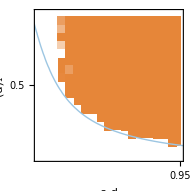

```mathematica
Show[Plotfix,p3]
```

Figure 3d

### 3.1 Loss of cooperation from abundance

We repeat the process but starting from a population of full cooperators. In that case, the initial phenotype express in the population is  z0={d_0, d_1, d_2, d_3,d^*, 1} with d_3 taking value between 0 and 1, and d_0, d_1and d_2 chosen at random. We keep track of the proportion of initial conditions that lead to z=0. As this procedure takes some computational time, we present the results generated from this procedure when plotting Fig. 3e.

```mathematica
NumericAnalysesLoss=Table[
Print[cdi];
values={n->4,β->1,Cc-> 0.3,δ->1.,u->1.,cd-> cdi} ;
βval=β/.values;
Ccval=Cc/.values;
ntest = n /. values;
cdtest = cd  /. values;
utest = u /. values;
valuesNeutral={n->ntest,β->0,Cc-> 0,cd->cdtest,u-> utest} ;
m[k_]:=fecdisp[d[n+1]] /(fecpatch[k](1-d[k])+fecdisp[d[n+1]] )/.δ->0;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.values;
solR2=Flatten[Solve[(R2 == ∑_(c0=0)^n (1-m[c0])^2(1/n+((n-1)/n)R2)Pk0[c0,d[n+1],n]/.valuesNeutral/.Functions//.valuesNeutral),R2]];
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) ;(* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.values/.Functions//.values;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,ntest+1},{i,1,3}]];
S=
Table[
D[w, d[1,k]]+ (n-1)R2 D[w, d[2,k]]/. solR2 /. monopop/.Functions//.values
,{k,0,ntest+1}];
(****** Creating the results file *******)
f="NumericAnalysesLoss_b_"<>TextString[βval]<>"_C_"<>TextString[Ccval]<>"_n_"<>TextString[ntest]<>".txt"/.values;
If[!FileExistsQ[f], (* If it does not exist yet, create it *)
CreateFile[f];
Close[f] //Quiet;
stream=OpenAppend[f];
];
Close[f] //Quiet;
Table[
res=
ParallelTable[
z0Random=Append[ Table[ RandomReal[{10^-5,1-10^-5}],{k,1,ntest+1}] ,1.];
z0= z0Random;
z0[[ntest+1]]= d0baseline;
z0[[ntest]]=dn1;
G =0.1 IdentityMatrix[ntest+2];
Δz[u_]:=Clip[ u+G.(S/. Table[d[k]-> u[[1+k]],{k,0,ntest+1}] ),{0.,1.}];
ngenmax=5000;
res0=NestWhile[Δz,z0,Abs[#1[[ntest+2]]-#2[[ntest+2]]]>10^-8&,2,ngenmax];
fix0=Last[res0];
Round[fix0,0.1]
,
{i,100}];
stream=OpenAppend[f]; (* Output stream *)
WriteLine[stream,StringRiffle[{cdi,dn1,Mean[res]} ]];
Close[f] //Quiet;
{cdi,dn1,Mean[res]} 
,{dn1,0.05,0.95,0.05}],{cdi,0.01,0.01,0.01}
];
NumericAnalysesLoss=Flatten[NumericAnalysesLoss,1]
```

0.01

$Aborted

```mathematica
(* This is the result we obtained running the above function once with 100 sets of initial trait values for each value of d1 and cd. If you run the above function, your results may differ slightly (due to the fact that the initial trait values will differ)*)NumericAnalysesLoss={{0.05,0.05,1.},{0.05,0.1,1.},{0.05,0.15,1.},{0.05,0.2,1.},{0.05,0.25,1.},{0.05,0.3,1.},{0.05,0.35,1.},{0.05,0.4,1.},{0.05,0.45,1.},{0.05,0.5,1.},{0.05,0.55,1.},{0.05,0.6,1.},{0.05,0.65,1.},{0.05,0.7,0.},{0.05,0.75,0.},{0.05,0.8,0.},{0.05,0.85,0.02},{0.05,0.9,0.},{0.05,0.95,0.03},{0.1,0.05,1.},{0.1,0.1,1.},{0.1,0.15,1.},{0.1,0.2,1.},{0.1,0.25,1.},{0.1,0.3,1.},{0.1,0.35,1.},{0.1,0.4,1.},{0.1,0.45,1.},{0.1,0.5,1.},{0.1,0.55,1.},{0.1,0.6,0.},{0.1,0.65,0.05},{0.1,0.7,0.01},{0.1,0.75,0.02},{0.1,0.8,0.04},{0.1,0.85,0.02},{0.1,0.9,0.028},{0.1,0.95,0.019},{0.15,0.05,1.},{0.15,0.1,1.},{0.15,0.15,1.},{0.15,0.2,1.},{0.15,0.25,1.},{0.15,0.3,1.},{0.15,0.35,1.},{0.15,0.4,1.},{0.15,0.45,1.},{0.15,0.5,0.157},{0.15,0.55,0.279},{0.15,0.6,0.152},{0.15,0.65,0.145},{0.15,0.7,0.138},{0.15,0.75,0.138},{0.15,0.8,0.133},{0.15,0.85,0.127},{0.15,0.9,0.187},{0.15,0.95,1.},{0.2,0.05,1.},{0.2,0.1,1.},{0.2,0.15,1.},{0.2,0.2,1.},{0.2,0.25,1.},{0.2,0.3,1.},{0.2,0.35,1.},{0.2,0.4,1.},{0.2,0.45,0.999},{0.2,0.5,1.},{0.2,0.55,1.},{0.2,0.6,1.},{0.2,0.65,1.},{0.2,0.7,1.},{0.2,0.75,0.995},{0.2,0.8,1.},{0.2,0.85,1.},{0.2,0.9,1.},{0.2,0.95,1.},{0.25,0.05,1.},{0.25,0.1,1.},{0.25,0.15,1.},{0.25,0.2,1.},{0.25,0.25,1.},{0.25,0.3,1.},{0.25,0.35,1.},{0.25,0.4,1.},{0.25,0.45,1.},{0.25,0.5,1.},{0.25,0.55,1.},{0.25,0.6,1.},{0.25,0.65,1.},{0.25,0.7,1.},{0.25,0.75,1.},{0.25,0.8,1.},{0.25,0.85,1.},{0.25,0.9,1.},{0.25,0.95,1.},{0.3,0.05,1.},{0.3,0.1,1.},{0.3,0.15,1.},{0.3,0.2,1.},{0.3,0.25,1.},{0.3,0.3,1.},{0.3,0.35,1.},{0.3,0.4,1.},{0.3,0.45,1.},{0.3,0.5,1.},{0.3,0.55,1.},{0.3,0.6,1.},{0.3,0.65,1.},{0.3,0.7,1.},{0.3,0.75,1.},{0.3,0.8,1.},{0.3,0.85,1.},{0.3,0.9,1.},{0.3,0.95,1.},{0.35,0.05,1.},{0.35,0.1,1.},{0.35,0.15,1.},{0.35,0.2,1.},{0.35,0.25,1.},{0.35,0.3,1.},{0.35,0.35,0.993},{0.35,0.4,1.},{0.35,0.45,1.},{0.35,0.5,1.},{0.35,0.55,1.},{0.35,0.6,1.},{0.35,0.65,1.},{0.35,0.7,1.},{0.35,0.75,1.},{0.35,0.8,1.},{0.35,0.85,1.},{0.35,0.9,1.},{0.35,0.95,1.},{0.4,0.05,1.},{0.4,0.1,1.},{0.4,0.15,1.},{0.4,0.2,1.},{0.4,0.25,1.},{0.4,0.3,1.},{0.4,0.35,1.},{0.4,0.4,1.},{0.4,0.45,1.},{0.4,0.5,1.},{0.4,0.55,1.},{0.4,0.6,1.},{0.4,0.65,1.},{0.4,0.7,1.},{0.4,0.75,1.},{0.4,0.8,1.},{0.4,0.85,1.},{0.4,0.9,1.},{0.4,0.95,1.},{0.45,0.05,1.},{0.45,0.1,1.},{0.45,0.15,1.},{0.45,0.2,1.},{0.45,0.25,1.},{0.45,0.3,0.997},{0.45,0.35,1.},{0.45,0.4,1.},{0.45,0.45,1.},{0.45,0.5,1.},{0.45,0.55,1.},{0.45,0.6,1.},{0.45,0.65,1.},{0.45,0.7,1.},{0.45,0.75,1.},{0.45,0.8,1.},{0.45,0.85,1.},{0.45,0.9,1.},{0.45,0.95,1.},{0.5,0.05,1.},{0.5,0.1,1.},{0.5,0.15,1.},{0.5,0.2,1.},{0.5,0.25,1.},{0.5,0.3,1.},{0.5,0.35,1.},{0.5,0.4,1.},{0.5,0.45,1.},{0.5,0.5,1.},{0.5,0.55,1.},{0.5,0.6,1.},{0.5,0.65,1.},{0.5,0.7,1.},{0.5,0.75,1.},{0.5,0.8,1.},{0.5,0.85,1.},{0.5,0.9,1.},{0.5,0.95,1.},{0.55,0.05,1.},{0.55,0.1,1.},{0.55,0.15,1.},{0.55,0.2,1.},{0.55,0.25,1.},{0.55,0.3,1.},{0.55,0.35,1.},{0.55,0.4,1.},{0.55,0.45,1.},{0.55,0.5,1.},{0.55,0.55,1.},{0.55,0.6,1.},{0.55,0.65,1.},{0.55,0.7,1.},{0.55,0.75,1.},{0.55,0.8,1.},{0.55,0.85,0.997},{0.55,0.9,1.},{0.55,0.95,1.},{0.6,0.05,1.},{0.6,0.1,1.},{0.6,0.15,1.},{0.6,0.2,1.},{0.6,0.25,1.},{0.6,0.3,1.},{0.6,0.35,1.},{0.6,0.4,1.},{0.6,0.45,1.},{0.6,0.5,1.},{0.6,0.55,1.},{0.6,0.6,1.},{0.6,0.65,1.},{0.6,0.7,1.},{0.6,0.75,1.},{0.6,0.8,1.},{0.6,0.85,1.},{0.6,0.9,1.},{0.6,0.95,1.},{0.65,0.05,1.},{0.65,0.1,1.},{0.65,0.15,1.},{0.65,0.2,1.},{0.65,0.25,1.},{0.65,0.3,1.},{0.65,0.35,1.},{0.65,0.4,1.},{0.65,0.45,1.},{0.65,0.5,1.},{0.65,0.55,1.},{0.65,0.6,1.},{0.65,0.65,1.},{0.65,0.7,1.},{0.65,0.75,1.},{0.65,0.8,1.},{0.65,0.85,1.},{0.65,0.9,1.},{0.65,0.95,1.},{0.7,0.05,1.},{0.7,0.1,1.},{0.7,0.15,1.},{0.7,0.2,0.99},{0.7,0.25,0.98},{0.7,0.3,0.98},{0.7,0.35,0.99},{0.7,0.4,0.98},{0.7,0.45,0.99},{0.7,0.5,0.99},{0.7,0.55,0.98},{0.7,0.6,0.99},{0.7,0.65,1.},{0.7,0.7,1.},{0.7,0.75,1.},{0.7,0.8,1.},{0.7,0.85,1.},{0.7,0.9,1.},{0.7,0.95,1.},{0.75,0.05,1.},{0.75,0.1,1.},{0.75,0.15,0.93},{0.75,0.2,0.93},{0.75,0.25,0.86},{0.75,0.3,0.91},{0.75,0.35,0.91},{0.75,0.4,0.9},{0.75,0.45,0.89},{0.75,0.5,0.91},{0.75,0.55,0.91},{0.75,0.6,0.94},{0.75,0.65,0.95},{0.75,0.7,0.87},{0.75,0.75,0.92},{0.75,0.8,0.89},{0.75,0.85,1.},{0.75,0.9,1.},{0.75,0.95,1.},{0.8,0.05,1.},{0.8,0.1,1.},{0.8,0.15,0.91},{0.8,0.2,0.86},{0.8,0.25,0.91},{0.8,0.3,0.89},{0.8,0.35,0.82},{0.8,0.4,0.88},{0.8,0.45,0.85},{0.8,0.5,0.77},{0.8,0.55,0.83},{0.8,0.6,0.84},{0.8,0.65,0.86},{0.8,0.7,0.86},{0.8,0.75,0.83},{0.8,0.8,0.87},{0.8,0.85,1.},{0.8,0.9,1.},{0.8,0.95,1.},{0.85,0.05,1.},{0.85,0.1,1.},{0.85,0.15,0.83},{0.85,0.2,0.77},{0.85,0.25,0.8},{0.85,0.3,0.85},{0.85,0.35,0.82},{0.85,0.4,0.77},{0.85,0.45,0.75},{0.85,0.5,0.78},{0.85,0.55,0.72},{0.85,0.6,0.78},{0.85,0.65,0.8},{0.85,0.7,0.71},{0.85,0.75,0.77},{0.85,0.8,0.78},{0.85,0.85,1.},{0.85,0.9,1.},{0.85,0.95,1.},{0.9,0.05,1.},{0.9,0.1,1.},{0.9,0.15,0.86},{0.9,0.2,0.69},{0.9,0.25,0.75},{0.9,0.3,0.69},{0.9,0.35,0.72},{0.9,0.4,0.824},{0.9,0.45,0.713},{0.9,0.5,0.74},{0.9,0.55,0.75},{0.9,0.6,0.73},{0.9,0.65,0.75},{0.9,0.7,0.71},{0.9,0.75,0.8},{0.9,0.8,0.8},{0.9,0.85,1.},{0.9,0.9,1.},{0.9,0.95,1.},{0.95,0.05,1.},{0.95,0.1,1.},{0.95,0.15,0.75},{0.95,0.2,0.75},{0.95,0.25,0.722},{0.95,0.3,0.685},{0.95,0.35,0.65},{0.95,0.4,0.745},{0.95,0.45,0.74},{0.95,0.5,0.575},{0.95,0.55,0.67},{0.95,0.6,0.77},{0.95,0.65,0.75},{0.95,0.7,0.663},{0.95,0.75,0.7},{0.95,0.8,0.717},{0.95,0.85,1.},{0.95,0.9,1.},{0.95,0.95,1.},{0.05,0.01,1.},{0.05,0.99,0.},{0.1,0.01,1.},{0.1,0.99,1.},{0.15,0.01,1.},{0.15,0.99,1.},{0.2,0.01,1.},{0.2,0.99,1.},{0.25,0.01,1.},{0.25,0.99,1.},{0.3,0.01,1.},{0.3,0.99,1.},{0.35,0.01,1.},{0.35,0.99,1.},{0.4,0.01,1.},{0.4,0.99,1.},{0.45,0.01,1.},{0.45,0.99,1.},{0.5,0.01,1.},{0.5,0.99,1.},{0.55,0.01,1.},{0.55,0.99,1.},{0.6,0.01,1.},{0.6,0.99,1.},{0.65,0.01,1.},{0.65,0.99,1.},{0.7,0.01,1.},{0.7,0.99,1.},{0.75,0.01,1.},{0.75,0.99,1.},{0.8,0.01,1.},{0.8,0.99,1.},{0.85,0.01,1.},{0.85,0.99,1.},{0.9,0.01,1.},{0.9,0.99,1.},{0.95,0.01,1.},{0.95,0.99,1.},{0.01,0.05,1.},{0.01,0.1,1.},{0.01,0.15,1.},{0.01,0.2,1.},{0.01,0.25,1.},{0.01,0.3,1.},{0.01,0.35,1.},{0.01,0.4,1.},{0.01,0.45,1.},{0.01,0.5,1.},{0.01,0.55,1.},{0.01,0.6,1.},{0.01,0.65,1.},{0.01,0.7,1.},{0.01,0.75,1.},{0.01,0.8,0.},{0.01,0.85,0.},{0.01,0.9,0.},{0.01,0.95,0.}};
```

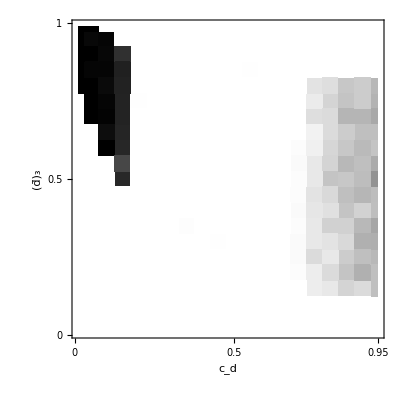

```mathematica
Plotfix=ListDensityPlot[NumericAnalysesLoss,InterpolationOrder->0,ColorFunction->GrayLevel,FrameTicks->{{{0,0.5,1},None},{{0,0.5,0.95},None}},PlotRangePadding->{{0.01,0.},0.01},LabelStyle->Directive[FontFamily->"Arial",FontSize->15,Black],FrameLabel->{Subscript[c, d],Rotate[Subscript[d̄, 3],-Pi/2]}]
```

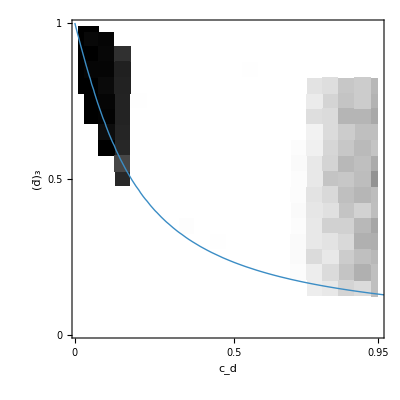

```mathematica
p2=ContourPlot[Evaluate[d1== 2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.n->4] ,{cd,0,1},{d1,0,1},ContourStyle->{Thick,Map[Lighter[blue,#]&,Reverse[Range[0,0.8,N[0.8/(ntest)]]]][[4]]}];
Show[Plotfix,p2]
```

Figure 3e